# Lab 7: Introduction to NIM

J.R. Powers-Luhn
jpowersl@vols.utk.edu
Station 5
Partner: Jeremy Watts

## Preamplifier

1. Properly plot the saved input/output traces (one set only) on a single plot.

```mathematica
datadir=NotebookDirectory[]<>"Data/Station5/";
```

```mathematica
inputData=Import[datadir<>"ALL0010.csv"][[17;;,1;;2]];
outputData=Import[datadir<>"ALL0005.csv"][[17;;,1;;2]];
scaleFactor=100;
outputData[[;;,2]]=outputData[[;;,2]]*scaleFactor;
inputData[[;;,1]]=inputData[[;;,1]]*1000; (* scale to ms *)
outputData[[;;,1]]=outputData[[;;,1]]*1000;(* scale to ms *)
```

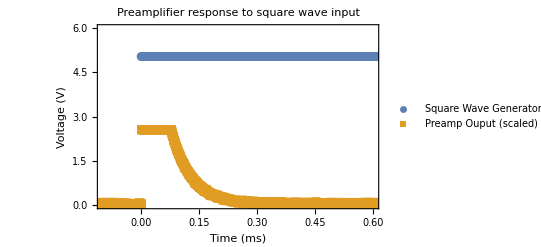

```mathematica
ListPlot[{inputData,outputData}, Axes->True, PlotRange->{{-0.1,0.6},{0, 6}},
Frame->True, ImageSize->Full,
FrameLabel->{Style["Time (ms)",Black,18],Style["Voltage (V)",Black,18]},
PlotLegends->Placed[{"Square Wave Generator", "Preamp Ouput (scaled)"},{0.85, 0.5}],
PlotMarkers->Automatic,
PlotLabel->Style["Preamplifier response to square wave input",Black,30],
FrameTicksStyle->Directive[{Black,18},{Black,18}]]
```

2. From the output decay of the preamplifier, fit an exponential to it and determine the decay time constant. Report the decay time constant in a text-style cell.

The decay occurs from approximately 0.1ms on, so the curve will be fit to data from the time range [0.1,0.4]

```mathematica
fitData=outputData[[13000;;14000,;;]];
fitData[[;;,2]]=fitData[[;;,2]]/scaleFactor;(* transform back for analysis *)
fitData[[;;,2]]=Log[fitData[[;;,2]]];
```

```mathematica
line=Fit[fitData,{1,t},t]
```

-2.66178-15.8308 t

```mathematica
15.830791415674563^-1
```

0.063168

The time constant of this decay is 0.063 ms^-1.

3. The preamplifier board used is the CR-150-R5 from CREMAT. Go to http://www.cremat.com/home/cr-150-r5-csp-evaluation-board/ and find the capacitance of the TEST capacitor.

From the PDF located at http://www.cremat.com/CR-150-R5.pdf, the value of the test capacitor is 1pF=10^-12 F

4. Using Q=CV, calculate the amount of injected charge into the preamplifier for the 5 input/output amplitude sets (i.e., find Q from the input voltage from the function generator).

```mathematica
capacitance=10^-12; (* Farads *)
```

```mathematica
amplitudeArray={1.000, 3.000, 5.000, 7.000, 9.000};
chargeInjected=capacitance*amplitudeArray
```

{1.×10^-12,3.×10^-12,5.×10^-12,7.×10^-12,9.×10^-12}

```mathematica
tableHeadings={"Input Voltage (V)", "Charge injected (pC)"};
dataTable = TableForm[Multicolumn[Join[amplitudeArray,chargeInjected*10^12],2]//First, TableHeadings->{None,tableHeadings}]
```

Input Voltage (V) | Charge injected (pC)
1. | 1.
3. | 3.
5. | 5.
7. | 7.
9. | 9.

The amount of injected charge for the 1.000V input was 1pC, for the 3.000V input was 3pC, for the 5.000V input was 5pC, for the 7.000V input was 7pC, and for the 9.000V input was 9pC.

5. From the injected charge and output voltage, from the preamplifier (saved traces), determine the gain of the preamplifier in units of mV/pC.

```mathematica
maxOutputVoltage[f_]:=Max[Import[datadir<>f][[17;;,2]]]
```

```mathematica
outputFiles={"ALL0001.csv", "ALL0002.csv", "ALL0003.csv", "ALL0004.csv", "ALL0005.csv"};
maxVolts=Table[1000*maxOutputVoltage[f],{f,outputFiles}](* mV *)
outputGain=maxVolts/(chargeInjected*10^12)
```

{13.2,25.6,25.6,25.6,25.6}

{13.2,8.53333,5.12,3.65714,2.84444}

```mathematica
tableHeadings=Append[tableHeadings,"Max Output Voltage (mV)"]
tableHeadings=Append[tableHeadings, "Gain (mV/pC)"]
```

{Input Voltage (V),Charge injected (pC),Max Output Voltage (mV)}

{Input Voltage (V),Charge injected (pC),Max Output Voltage (mV),Gain (mV/pC)}

```mathematica
TableForm[Multicolumn[Join[amplitudeArray,chargeInjected*10^12,maxVolts,outputGain],4]//First,TableHeadings->{None,tableHeadings}]
```

Input Voltage (V) | Charge injected (pC) | Max Output Voltage (mV) | Gain (mV/pC)
1. | 1. | 13.2 | 13.2
3. | 3. | 25.6 | 8.53333
5. | 5. | 25.6 | 5.12
7. | 7. | 25.6 | 3.65714
9. | 9. | 25.6 | 2.84444

6. Report the data (input voltage, injected charge, output voltage, and calculated gain) in a table within the Mathematica notebook as done in a previous laboratory exercise.

```mathematica
TableForm[Multicolumn[Join[amplitudeArray,chargeInjected*10^12,maxVolts,outputGain],4]//First,TableHeadings->{None,tableHeadings}]
```

Input Voltage (V) | Charge injected (pC) | Max Output Voltage (mV) | Gain (mV/pC)
1. | 1. | 13.2 | 13.2
3. | 3. | 25.6 | 8.53333
5. | 5. | 25.6 | 5.12
7. | 7. | 25.6 | 3.65714
9. | 9. | 25.6 | 2.84444

7. The preamplifier used was either a CR-110, CR-111, CR-112, CR-113 (http://www.cremat.com/home/charge-sensitive-preamplifiers/). From the table of data and calculated fall time, determine what preamplifier was used.

Based on the data collected in the lab, the preamplifier appears to be the CR-112, which has a stated fall time of 50μs=0.050ms and a gain of 13mV/pC.

Amplifier Linearity